## Polyhedron Edge-Roll

## Problem Input

```mathematica
polyhedronType= "Cube";
gc=PolyhedronData[polyhedronType,"GraphicsComplex"]//N;
faceIndices = PolyhedronData[polyhedronType,"FaceIndices"]; (*faces represented by indices*)
angles = PolyhedronData[polyhedronType,"DihedralAngles"];
angle = angles[[1]];

aim2D = {5,7};
r=7.5;
(*plot range global*)
```

```mathematica
Graphics3D[gc,ImageSize->Small, Axes-> True]
```

-Graphics3D-

## Modify Input

### label vertices

```mathematica
verts=gc⟦1⟧;
text=MapThread[Text[#1,#2]&,{Range[Length[verts]],verts}];
```

### find base; if base is a point, rotate for it to be a face

#### basic face-base

```mathematica
(*find the lowest Z-value*)
min = Infinity;
vertsZ = verts;
For [i=1, i<=Length[verts],i++,
num = verts[[i]][[3]];
vertsZ[[i]] = num;
If[ num<min, min=num,Null];
];
```

```mathematica
aim =Point[{aim2D[[1]],aim2D[[2]], min}];
```

```mathematica
Graphics3D[{
{Opacity[0.75],gc}
,{Blue,text}
}
(*,Boxed->False*)
, Axes -> True
]
```

-Graphics3D-

```mathematica
(*find the lowest point and store it in "base"*)
base ;
facesWithBase={};
For [i=1, i≤Length[faceIndices], i++,
isBase = True;
For[j=1, j≤ Length[faceIndices[[i]]], j++,
vertexIndex = faceIndices[[i,j]];
If[vertsZ[[vertexIndex]] ≠ min
,
isBase=False;
,
base = {vertexIndex};
facesWithBase =  Append[facesWithBase,faceIndices[[i]]];
]
];
If[isBase, base =faceIndices[[i]]; Break[], Null];
];
```

#### point-base and rotation

```mathematica
(*Deal with cases where the base is not a face but an edge or a point*)
If[Length[base]==1,
baseIndex = base[[1]];

baseCoord = verts[[baseIndex]];

(*pick a random face to fall down to*)
face = facesWithBase[[1]];

(*get the corordinate of the face vertices; get another vertex on the face that is not the current base*)
faceCoord  =face;
vertexNotbase = 1;
For [i =1, i≤Length[face],i++,
If [face[[i]] != baseIndex,
vertexNotBase = face[[i]],
Null];
faceCoord[[i]] = verts[[face[[i]]]];
];

verCoord = verts[[vertexNotBase]];

(*pick an x different from base.x*)
x = baseCoord[[1]]+1;
y;
result = Solve[
{x,y,min}∈InfinitePlane[faceCoord] && {x,y,min}∈InfinitePlane[{{0,0,min},{1,0,min},{0,1,min}}],y];
(*should only have one result, so following simply writes result[[1]];*)
pt2 = Point[{x,y, min}/.result[[1]]];

axisPt1 = baseCoord;
axisPt2 = pt2[[1]];
ptOnFace = verCoord;

result=RotToFace[axisPt1,axisPt2,ptOnFace,face,gc];
graph=result[[1]];
 base = result[[2]];

base=face;
verts = graph[[1,1,2,1]];
gc = graph[[1,1,2]];

g=Graphics3D[{
{Opacity[0.75],gc,
Red, PointSize[Large],aim,
Green,InfinitePlane[{{0,0,min},{1,0,min},{0,1,min}}],}
,{Blue,graph[[1,2,2]]}
}
(*,Boxed->False*)
, Axes -> True
,PlotRange->{{-2,5},{-2,5},{min-0.5,-min+0.5}}
];
Print[g];
];
```

### final graph

```mathematica
graph=PlotGraph[gc, aim, text];
Print[graph];
```

-Graphics3D-

## Helper Functions

### BaseIndexToPoly[baseIndexList_]

- change a list with base indices to a corresponding polygon.

```mathematica
BaseIndexToPoly[baseIndexList_] := Module[{i,basePoly},
basePoly = baseIndexList;
For[i=1, i≤Length[baseIndexList],i++
, baseCoord=verts[[ basePoly[[i]] ]]; 
basePoly[[i]] = {baseCoord[[1]], baseCoord[[2]]}
];
Return[basePoly];
];
```

### TestPoint[poly_,pt_]

- test if a point is in a polygon.

```mathematica
TestPoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0;
(*https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon
*)
```

### BaseContainsPoint[baseIndexList_, aim3D_]

- check if aim is cover by the base.

```mathematica
BaseContainsPoint[base_, aim_] := Module[{basePoly, baseCoord, },
basePoly=BaseIndexToPoly[base];
aim2D = {aim[[1,1]], aim[[1,2]]};
Return[TestPoint[basePoly,aim2D]];
];
```

### FindAimVector[baseCoordList_, aim3D_]

- find the closest point on base to aim and return the vector from this point to aim.

```mathematica
FindAimVector[baseCoord_, aim_] := Module[{i,aim2D,baseCoord2D, line, baseRegion, closestPoint, aimVector},
aim2D = {aim[[1,1]], aim[[1,2]]};

baseCoord2D = baseCoord;
For[i=1, i≤Length[baseCoord], i++,
baseCoord2D[[i]] = {baseCoord[[i,1]], baseCoord[[i,2]]}
];

line = Line[Append[Range[Length[baseCoord]],1]];
baseRegion=Region[BoundaryMeshRegion[baseCoord2D,line]];
closestPoint = RegionNearest[baseRegion, aim2D];
aimVector = aim2D-closestPoint;
Return [aimVector];
];
```

### FindNextBaseAndAxis[baseIndexList_, baseCoordList_ , aim2D_]

- find the index of the next axis (as a list with two edge endpoints) that provides a largest step.

```mathematica
FindNextBaseAndAxis[base_, baseCoord_ , aim2D_] := Module[{baseCoord1, base1,minDistance,edge,axisPt1,axisPt2,faceIndex,ptOnFaceIndex, ptOnFace, result, aimVector,dis, i, j, k, newBase, graph, newVerts},

base1 = Append[base, base[[1]]];
baseCoord1 = Append[baseCoord, baseCoord[[1]]];
minDistance= Infinity;

(*for each edge on the base*)
For[i=1,i≤ Length[base],i++,
edge = {base1[[i]] , base1[[i+1]]};
axisPt1 = baseCoord1[[i]];
axisPt2 = baseCoord1[[i+1]];

faceIndex = BaseChangeRot[base, base1[[i]], base1[[i+1]]] ;

result = RotToNewBase[faceIndex,{base1[[i+1]], base1[[i]]}, gc];

newVerts = result[[1,1,1,2,1]];

faceCoord =faceIndex;
For[k=1, k≤Length[faceIndex], k++,
faceCoord[[k]] = newVerts[[faceIndex[[k]]]];
];
aimVector = FindAimVector[faceCoord, aim];
dis = Norm[aimVector] ;
If[dis<minDistance, minDistance=dis; newBase=faceIndex; graph=result[[1]], Null];
];
Return[{newBase,graph}];
];
```

### VertexIndicesToCoords

```mathematica
VertexIndicesToCoords[indexList_, verts_] := Module[{coordList},
coordList= {};
For[i=1, i≤Length[indexList], i++,
coordList= Append[coordList,verts[[ indexList[[i]] ]] ];
];
Return[coordList];
];
```

### VertexCoordsTo2d

```mathematica
VertexCoordsTo2d[verCoords_] := Module[{verCoords2d},
verCoords2d = verCoords;
For[i=1, i≤Length[verCoords],i++,
verCoords2d[[i]] = {verCoords[[i,1]], verCoords[[i,2]]};
];
Return[verCoords2d];
];
```

### ToNextLayer

```mathematica
ToNextLayer[currDodecDataList_, coveredList_] := Module[{
nextDodecDataList,newCoveredGraph,currGc,verts,baseIndex,baseIndex1,baseCoord,baseCoord1,faceIndex,graphAndBase, graph, newBase, newVerts, newBaseCoord,i, j,newBaseCoord2d, newCoveredList, newLayerList},
nextDodecDataList = {};
newCoveredList = coveredList;
newLayerList = {};

For[i=1, i≤Length[currDodecDataList], i++,
currGc = currDodecDataList[[i,1,1, 1,2]];
verts = currGc[[1]];
baseIndex = currDodecDataList[[i,2]];
baseCoord =VertexIndicesToCoords[baseIndex, verts];
baseIndex1 = Append[baseIndex, baseIndex[[1]]];
baseCoord1 = Append[baseCoord, baseCoord[[1]]];

(*for each edge on the base*)
For[j=1,j≤ Length[baseIndex],j++,
verts = currGc[[1]];
newBase=BaseChangeRot[baseIndex,baseIndex1[[j]], baseIndex1[[j+1]]];

graphAndBase = RotToNewBase[newBase,{baseIndex1[[j+1]], baseIndex1[[j]]}, currGc, verts];
graph = graphAndBase[[1]];
verts = graph[[1,1,2,1]];

nextDodecDataList = Append[nextDodecDataList, {graph, newBase}];
newBaseCoord = VertexIndicesToCoords[newBase,verts];
newBaseCoord2d = VertexCoordsTo2d[newBaseCoord];
newLayerList = Append[newLayerList, Polygon[newBaseCoord2d]];
];
];
newCoveredList = Append[newCoveredList, newLayerList];
Return [{nextDodecDataList, newCoveredList}];
];
```

### PlotGraph[gc_, aim3D_, text_]

-  plot a graph of this specific use of project, with polyhedron, labelling and aim.

```mathematica
PlotGraph[gc_, aim_, text_] := Module[{g},
g=Graphics3D[{
{Opacity[0.75],gc,
Green,InfinitePlane[{{0,0,min},{1,0,min},{0,1,min}}]}
,{Blue,text}
}
(*,Boxed->False*)
, Axes -> True
,PlotRange->{{-2,r},{-2,r},{min-0.5,-min+0.5}}
];
Return[g];
];
```

### EdgeRot[θ_,v1Coord_,v2Coord_,gc_]

- rotate polyhedron gc for angle theta by an axis (v1,v2) and return plotted graph.

```mathematica
EdgeRot[θ_,a_,b_,gc_]:=Module[{rot,g,text,verts,gcrot},
(*gcrot=rotated version of gc*)
gcrot=gc;
verts=gc⟦1⟧;
rot=RotationTransform[θ,b-a,a];
verts=Map[rot[#]&,verts];
gcrot⟦1⟧=verts;
(*gcrot⟦2⟧ remains the same*)
text=MapThread[Text[#1,#2]&,{Range[Length[verts]],verts}];
g=PlotGraph[gcrot, aim, text];

Return [g];
];
```

### BaseChangeRot[baseIndexList_, vi1_, vi2_]

- return the index list of new base after rotation, used with EdgeRot.

```mathematica
BaseChangeRot[base_, vi1_, vi2_] := Module[{i, newBase},
For[i=1, i≤Length[faceIndices], i++,
face = faceIndices[[i]];
If[
ContainsAll[face,{vi1,vi2}]&&face≠base
,newBase=face
, Null];
];
Return[newBase];
];
```

### RotToFace[axisPt1, axisPt2, ptOnFace, face, gc]

```mathematica
RotToFace[axisPt1Coord_,axisPt2Coord_,ptOnFace_, face_,gc_] := Module[{ptOnPlane, v,w,rotAngle, newBase, graph,r},

(*find a point on the plane the face is rotating onto. Direction matters. *)
r= RotationTransform[1,{0,0,-1}, axisPt1Coord];
ptOnPlane = r[axisPt2Coord];

v=ptOnFace-axisPt1Coord;
w = ptOnPlane-axisPt1Coord;

rotAngle = DihedralAngle[{axisPt1Coord,axisPt2Coord},{v,w}];

graph = EdgeRot[rotAngle,axisPt1Coord,axisPt2Coord,gc];
newBase=face;
Return [{graph, newBase}];
];
```

### RotToNewBase[newBase,axisIndexList,gc]

```mathematica
RotToNewBase[newBase_,axisIndexList_, gc_, verts_] := Module[{j,axisi1 ,axisi2, ptOnFaceIndex, ptOnFaceCoord},
axisi1 = axisIndexList[[1]];
axisi2 = axisIndexList[[2]];

(*find another point that is not the rotation edge on the potential base.*)
For[j=1, j≤Length[newBase], j++,
If[newBase[[j]]≠ axisi1&& newBase[[j]]≠ axisi2, 
ptOnFaceIndex =newBase[[j]] ; Break[], Null];
];

ptOnFaceCoord = verts[[ptOnFaceIndex]];

result=RotToFace[verts[[axisi1]],verts[[axisi2]],ptOnFaceCoord,newBase,gc];
Return[result];
];
```

## Perform Rotations

### initial values

```mathematica
g=PlotGraph[gc, aim, text];
Print[g];
```

-Graphics3D-

```mathematica
currDodecDataList = {{g, base}};
coveredList  ={};
normalList={};
prevList = {};
(*coveredList = {{Green, Point[{0,0}]}};*)
visitedList = {Polygon[BaseIndexToPoly[base]]};
layer = 0;
```

### loops of rotations

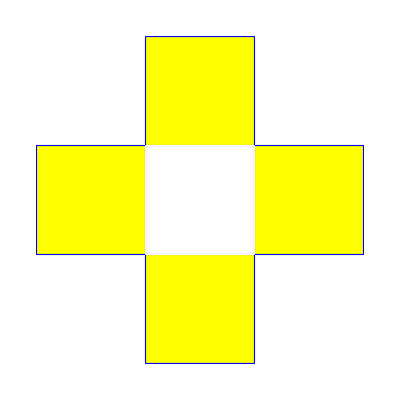

1

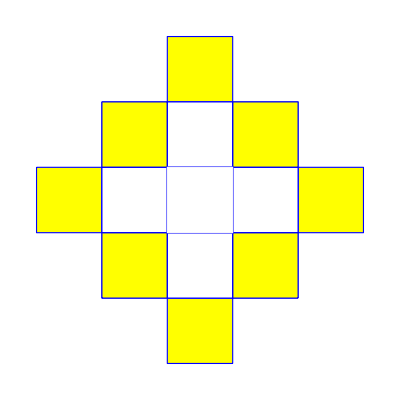

2

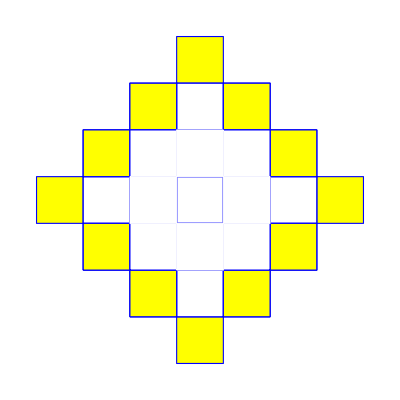

3

```mathematica
While[layer≤2,
normalList = prevList;
prevList = coveredList;
DodecAndRegionNextLayer= ToNextLayer[currDodecDataList ,coveredList];
currDodecDataList = DodecAndRegionNextLayer[[1]];
coveredList = DodecAndRegionNextLayer[[2]];
Print[Graphics[{
EdgeForm[{Thick, Blue}],
{Opacity[1], Yellow,coveredList}, 
{Opacity[1], White,prevList}, 
EdgeForm[{Thin, White}],
{Opacity[1], White,visitedList}, 
{Opacity[1], White, normalList}}]];
layer = layer+1;
Print[layer];
];
```